# Challenges - W8

## Cameron Embree - 3/13/14

Challenge 1: Find the singular value decompostion of the matrix a below and make a scree plot of the singular values.

```mathematica
(*Challenge 1 solution by:*)
a={{0.1521,0.39780000000000004,1.02,0.39,1},{0.1024,0.304,0.95,0.32,1},{0.0729,0.23490000000000003,0.87,0.27,1},{0.0484,0.1694,0.77,0.22,1},{0.0324,0.1206,0.67,0.18,1},{0.0225,0.084,0.56,0.15,1},{0.016900000000000002,0.0572,0.44,0.13,1},{0.0144,0.036,0.3,0.12,1},{0.016900000000000002,0.020800000000000003,0.16,0.13,1},{0.0225,0.0015,0.01,0.15,1}};
```

```mathematica
{u,w,v}=SingularValueDecomposition[a];
w//MatrixForm
```

(3.78604 | 0. | 0. | 0. | 0.
0. | 0.944923 | 0. | 0. | 0.
0. | 0. | 0.208913 | 0. | 0.
0. | 0. | 0. | 0.0230432 | 0.
0. | 0. | 0. | 0. | 0.00549953
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

Challenge 2:  Construct a matrix for fitting a degree 15 polynomial to sin(x) on 200 equally spaced points on the interval [0,1] using different numbers of the first 200 singular values.  Use the tolerence option in mathematicas singularvaluedecompostion fuction to throw away small singular values.

```mathematica
(*Challenge 2 solution by:*)
```

```mathematica
f[x_]:={1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14};
mat=Table[f[i],{i,0,1,(1/200)//N}];


k=8;
{u,w,v}=SingularValueDecomposition[mat,k];
w//MatrixForm
```

(19.3513 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 9.36475 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 3.43807 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.08223 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.301961 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0754982 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0169798 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00343455)

Challenge 3: Find a rank 10 approximation of a greyscale image imported from the internet.

```mathematica
(*Challenge 3 solution by:*)
```

-Graphics-

256

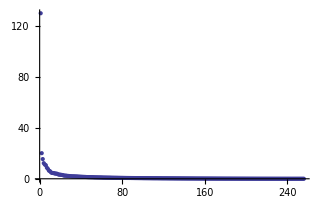

-Graphics-

```mathematica
img=Import["http://meesoft.logicnet.dk/Analyzer/help/Lenna.jpg"]

MatrixRank[ImageData[img]]
ImageData[img];
{u,w,v}=SingularValueDecomposition[ImageData[img]];
ListPlot[Diagonal[w],PlotRange->Full]
{u2,w2,v2}=SingularValueDecomposition[ImageData[img],10];(* First 10 singular values *)
Image[u2.w2.Transpose[v2]] (* Reconstruct a but with the first 50 singular values *)
```

Challenge 4:  Find the first, second, third, fourth and fifth degree polynomial fits to the following data and plot the data and polynomials using SVD. {{0,.7829},{.1,.8052},{.2,.5753},{.3,5201},{.4,.3783},{.5,.2923},{.6,1695},{.7,.0842},{.8,.0415},{.9,.009},{0,1}}

```mathematica
(*Challenge 4 solution by:*)
```

{{0,0,0,0},{0.1,0.00001,0.0001,0.00001},{0.2,0.00032,0.0016,0.00032},{0.3,0.00243,0.0081,0.00243},{0.4,0.01024,0.0256,0.01024},{0.5,0.03125,0.0625,0.03125},{0.6,0.07776,0.1296,0.07776},{0.7,0.16807,0.2401,0.16807},{0.8,0.32768,0.4096,0.32768},{0.9,0.59049,0.6561,0.59049},{0,0,0,0}}

{0.7829,0.8052,0.5753,5201,0.3783,0.2923,1695,0.0842,0.0415,0.009,1}

{5972.42,22107.,-47757.3,22107.}

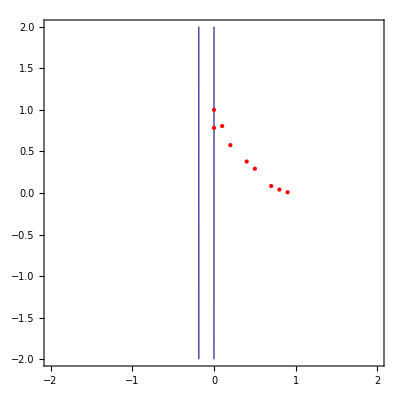

```mathematica
data={{0,.7829},{.1,.8052},{.2,.5753},{.3,5201},{.4,.3783},{.5,.2923},{.6,1695},{.7,.0842},{.8,.0415},{.9,.009},{0,1}};
aa={#[[1]],#[[1]]^2*#[[1]]^3,#[[1]]^4,#[[1]]^5} &/@data
b=#[[2]] & /@data

LeastSquares[aa,b]

plotPoly[{a_,b_,c_,d_,e_},wind_]:=ContourPlot[a*x+b*x^2+c*x^3+d*x^4+e*x^5==y,{x,-wind,wind},{y,-wind,wind}]

Show[plotPoly[LeastSquares[aa,b],2],ListPlot[data,PlotStyle->Red]]
```

Challenge 5:  Create the rank 3 approximation the matrix a in Challenge 1.

```mathematica
(*Challenge 5 solution by:*)
```

```mathematica
a={{0.1521,0.39780000000000004,1.02,0.39,1},{0.1024,0.304,0.95,0.32,1},{0.0729,0.23490000000000003,0.87,0.27,1},{0.0484,0.1694,0.77,0.22,1},{0.0324,0.1206,0.67,0.18,1},{0.0225,0.084,0.56,0.15,1},{0.016900000000000002,0.0572,0.44,0.13,1},{0.0144,0.036,0.3,0.12,1},{0.016900000000000002,0.020800000000000003,0.16,0.13,1},{0.0225,0.0015,0.01,0.15,1}}

(* Rank 3 approx *)
{u,w,v}=SingularValueDecomposition[a,3];
w//MatrixForm

aa=u.w.Transpose[v]
```

{{0.1521,0.3978,1.02,0.39,1},{0.1024,0.304,0.95,0.32,1},{0.0729,0.2349,0.87,0.27,1},{0.0484,0.1694,0.77,0.22,1},{0.0324,0.1206,0.67,0.18,1},{0.0225,0.084,0.56,0.15,1},{0.0169,0.0572,0.44,0.13,1},{0.0144,0.036,0.3,0.12,1},{0.0169,0.0208,0.16,0.13,1},{0.0225,0.0015,0.01,0.15,1}}

(3.78604 | 0. | 0.
0. | 0.944923 | 0.
0. | 0. | 0.208913)

{{0.147424,0.394132,1.02034,0.396443,0.999237},{0.105323,0.304011,0.950055,0.318363,1.00016},{0.076876,0.238091,0.869705,0.264446,1.00066},{0.0508422,0.173702,0.769546,0.214135,1.00073},{0.0322452,0.123385,0.669673,0.177168,1.00038},{0.0201408,0.0838041,0.559977,0.151517,0.999847},{0.0137182,0.0534129,0.440379,0.135737,0.9993},{0.0122618,0.029302,0.300739,0.128206,0.998947},{0.017541,0.0177298,0.16037,0.13286,0.999604},{0.0250121,0.00860216,0.00922125,0.141162,1.00113}}